```mathematica
Clear["Global`*"]
```

```mathematica
NN=201;
h=rMax/NN;
```

```mathematica
nMat=1.444;
k0=2Pi/1.55;
l=0;
rMax=100;
rCore=50/2;
percn=0.0036;
c=3*10^8/1000/10^12;(*скорость света в км/пс*);
```

```mathematica
V=((2*π*rCore/1.55)^2*2*nMat*percn*nMat)^0.5;
```

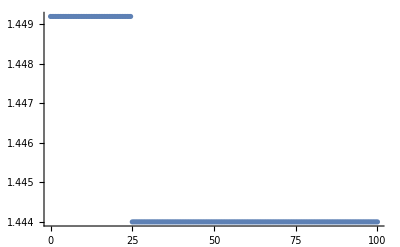

```mathematica
RIP=Array[(percn*HeavisideTheta[rCore-h#]+1)nMat&,NN];
ListPlot[RIP, DataRange->{0,rMax}]
```

```mathematica
D1=DiagonalMatrix[ConstantArray[-1/2,NN-1],-1]+DiagonalMatrix[ConstantArray[1/2,NN-1],1];
D1[[1]]=PadRight[{-3/2,2,-1/2},NN];
D1[[-1]]=PadLeft[{1/2,-2,3/2},NN];
D2=Normal[SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{NN,NN}]];
D2[[1]]=PadRight[{2,-5,4,-1},NN];
D2[[-1]]=PadLeft[{-1,4,-5,2},NN];
DivByr=Array[1/h/#&,NN];
shturmop=D2/h^2+1/h D1 DivByr-l^2DivByr^2 IdentityMatrix[NN]+k0^2 RIP^2 IdentityMatrix[NN];
{β,Modes}=Eigensystem[shturmop];
β=Sqrt[β];
```

```mathematica
(*Пункт 3*)
```

```mathematica
(*Селлмейер*)
a1=0.69616630;
a2=0.40794260;
a3=0.89747940;
l1=0.068404300;
l2=0.11624140;
l3=9.8961610;
ϵ=1+a1*λ^2/(λ^2-l1^2)+a2*λ^2/(λ^2-l2^2)+a3*λ^2/(λ^2-l3^2);
n:=ϵ^(1/2);
```

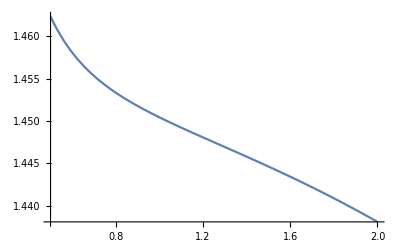

```mathematica
Plot[n,{λ,0.5,2}]
```

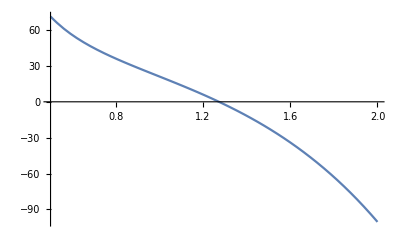

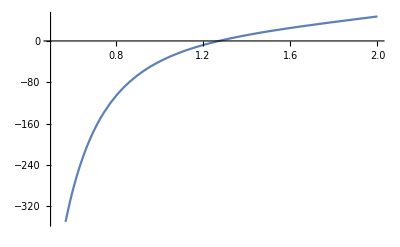

```mathematica
β2=10^-9*λ^3*D[n,{λ,2}]/(2*π*c^2);(*коэффициент 10^-9 нужен для того, чтобы перевести в пс^2/км*)
Plot[β2,{λ,0.5,2}]
d=β2*(-2*π*c/λ^2)*10^6;
Plot[d,{λ,0.5,2}]
(*Красные компоненты движутся быстрее, чем синии в области нормальной дисперсии*)
```

```mathematica
(*Пункт 4*)
```

```mathematica
(*1 этап отсева: эффективный показатель преломления находится между максимальным и минимальным показателем преломления ступенчатого профиля, также отсутствует мнимая часть*)
```

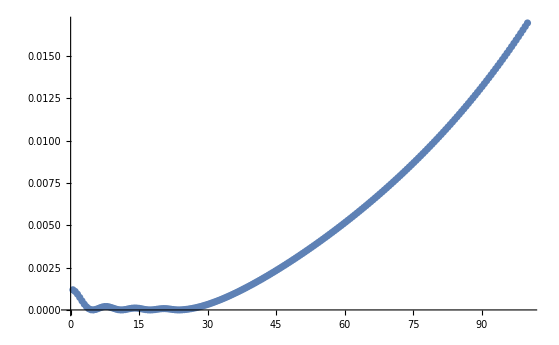

```mathematica
n=5;
TrueModesNEff=Chop[Select[β/k0,((Re[#]>nMat)&&(Re[#]<nMat*(1+percn))&&(Im[#]<10^-10))&] ];
svect=Table[First[NullSpace[shturmop-(TrueModesNEff[[i]]*k0)^2*IdentityMatrix[NN]]],{i,Length[TrueModesNEff]}];
ListPlot[Abs[svect[[n]]]^2,PlotRange->All,DataRange->{h,rMax}]
Dimensions[TrueModesNEff];
```

```mathematica
(*2 этап - убираем моды, амплитуда которых вблизи края волокна не близка к нулю, а также амплитуды производная положительна*)
```

```mathematica
βRes={};
att=100;(*коэффициент, показывающий во сколько раз допустимо отличие по интенсивности*)
maxDer=100;
```

```mathematica
TrueModesNEff
```

{1.44903,1.44833,1.44709,1.44536,1.444}

```mathematica
For[i=1,i<Length[svect],i++,
(*производная*)
dE=ListCorrelate[{-1,1},svect[[i]]];
dE=Insert[dE,svect[[i]][[-1]]-svect[[i]][[-2]],-1];
dE=dE/h;

If[MatchQ[Max[Abs[svect[[i]]^2]]/att-Abs[svect[[i]][[-5;;-1]]^2],{__?Positive}]&& MatchQ[Max[Abs[dE]]/maxDer-dE[[-5;;-1]],{__?Positive}],
βRes=Insert[βRes,TrueModesNEff[[i]],-1];
]
]
```

```mathematica
βRes
```

{1.44903,1.44833,1.44709,1.44536}

```mathematica
numbers=Table[Position[Re[β/k0],βRes[[i]]][[1]],{i,Length[βRes]}]
```

{{1},{2},{3},{4}}

```mathematica
(*Пункт 6*)
```

```mathematica
test={1,5,3,4};
```

```mathematica
1-test
```

{0,-4,-2,-3}

```mathematica
lok[x_]:=If[x>0,True,False];
```

```mathematica
MatchQ[test,{__?lok}]
```

True

```mathematica
Position[test,_?lok]
```

{{1},{2},{3},{4}}